```mathematica
(* Copyright (C) 2020 Craciun Alexandru

This package is free: you can redistribute it and/or modify it under the
 terms of the GNU General Public License as published by the Free Software
 Foundation, either version 3 of the License, or (at your option) any
 later version. This program is distributed in the hope that it will be
 useful, but WITHOUT ANY WARRANTY; without even the implied warranty of
 MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See the GNU General
 Public License for more details. You should have received a copy of the
 GNU General Public License along with this program
if not, see <https://www.gnu.org/licenses/>.

 Author: CRACIUN Alexandru, e-mail:alexandru.craciun@inflpr.ro

 Please send me an e-mail if you have found a mistake or have questions. *)

(*This code is compatible with Mathematica 10 or later versions.*)

(*Mathematica is (C) Copyright 1988-2020 Wolfram Research, Inc. 
Protected by copyright law and international treaties. 
Unauthorized reproduction or distribution subject to severe civil and criminal penalties.
Mathematica is a registered trademark of Wolfram Research, Inc. 
*)
```

```mathematica
(*Some Vector Graphics were replaced by Images to decrease the file size. *)
SetOptions[EvaluationNotebook[],AutoStyleOptions->{"CommentStyle"->{FontWeight->Plain,FontColor->Darker[Red],ShowAutoStyles->False,ShowSyntaxStyles->False,AutoNumberFormatting->False,FontFamily->"Consolas"}}]
```

```mathematica
(*Geometrical Optics + Physical Optics *)

(*Spherical Lens Ex. 2.1 *)

(*A simple optical system consisting of one spherical lens is defined. *)
Options[optSystem]={"tiltedRays"-> False};
optSystem[rayTiltStart_,rayCoordinateStart_,focusCorrection_,distBefore_,OptionsPattern[]]:=Module[{},

refractiveIndex1=refIndexNBK7800;(*The refractive index of the lens made of N-BK7. *)
centerThickness1=2.4 mm;(*Central thickness of the lens. *)

curvRadius1=15.5mm;(*Radius of curvature of the first surface of the lens. *)

focalDistance1=0. mm+focusCorrection;(*The distance between the second (plane) surface of the lens and the focal plane. *)
(*This value is set arbitrarly for the first Ray Tracing, then is determined using FindFocus. *)
surface1[x_,y_]=distBefore1+SLz[x,y,curvRadius1,0];(*Spherical first surface. *)
surface2[x_,y_]=surface1[0,0]+centerThickness1;(*Plane second surface. *)
DxSurface1[x_,y_]=D[surface1[x,y],x];(*The derivatives, which are necessary for finding the intersection with the surface and direction of the refracted rays.*)
DySurface1[x_,y_]=D[surface1[x,y],y];
DxSurface2[x_,y_]=D[surface2[x,y],x];
DySurface2[x_,y_]=D[surface2[x,y],y];

If[OptionValue["tiltedRays"]==False,

intersectionA={#[[1]],#[[2]],0}&/@rayCoordinateStart;,
intersectionA={#[[1]],#[[2]],#[[3]]}&/@rayCoordinateStart; ];

intersectionB=SurfaceIntersection[intersectionA,{},rayTiltStart][surface1[0,0]&,0&,0&];(*This is a plane surface tangent to the first surface. Intersection is accurate in 1 iteration. *)

intersection1=SurfaceIntersection[intersectionA,{},rayTiltStart][surface1,DxSurface1,DySurface1];
Do[intersection1=SurfaceIntersection[intersection1,{},rayTiltStart][surface1,DxSurface1,DySurface1],10];
(*This is the first surface of the lens. Because this surface is not plane, multiple recursions are needed. *)
direction1=DirectionIn[intersection1,rayTiltStart,refractiveIndex1][DxSurface1,DySurface1];(*Snell Law applied for the first surface. *)

intersection2=SurfaceIntersection[intersection1,{},direction1][surface2,DxSurface2,DySurface2];(*The last plane surface before the focal plane is actually the second plane surface of the lens. *)
direction2=DirectionOut[intersection2,direction1,refractiveIndex1][DxSurface2,DySurface2];

surface3[x_,y_]=Fit[intersectionA,{x,y},{x,y}]+5 mm;(*A plane surface perpendicular on the chief-ray, placed at 2.6 mm after the lens. *)
DxSurface3[x_,y_]=D[surface3[x,y],x];
DySurface3[x_,y_]=D[surface3[x,y],y];

intersection3=SurfaceIntersection[intersection2,{},direction2][surface3,DxSurface3,DySurface3];

intersectionC=SurfaceIntersection[intersection2,{},direction2][(surface2[0,0]+focalDistance1)&,0&,0&](*Image Plane/ Focal Plane. *)

]
```

Position of the Image Plane is at:

41.101

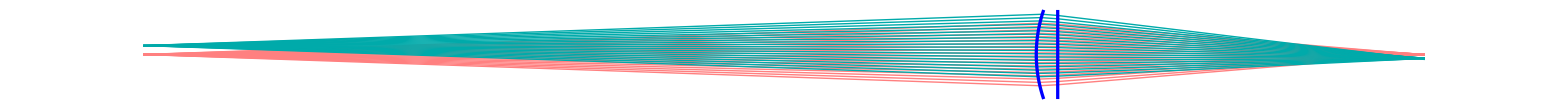

```mathematica
(*Image Formation. *)
distBefore1=100 mm;

(*1*)tStart={#[[1]],#[[2]],√(1-#[[1]]^2-#[[2]]^2)}&/@LineGrid[2 °,400];

(*2*)rcStart={0,0}&/@tStart;(*This (1,2) generates a set of rays that emerge from one point (point-source). tStart -> input direction vectors, rcStart -> input coordinates (on axis). *)

optSystem[tStart,rcStart,0 mm,distBefore1];(*This calls the function optSystem that Trace the Rays through the System. *)

Print["Position of the Image Plane is at: "]
ff=FindFocusLine[intersectionC,direction2]/mm(*This finds the position of the Image Plane. *)

tStart={#[[1]],#[[2]],√(1-#[[1]]^2-#[[2]]^2)}&/@LineGrid[2°,20];

rcStart={0,0}&/@tStart;(*tStart -> input direction vectors, rcStart -> input coordinates (off axis). *)

optSystem[tStart,rcStart,ff mm,distBefore1];(*This calls the function optSystem that Trace the Rays through the System, now that the position of the Image Plane is known, in order to draw the system. *)

llp1=ListLinePlot[Transpose[#[[All,{3,1}]]&/@{intersectionA,intersection1,intersection2,intersectionC}]/mm,AspectRatio->10/(distBefore1/mm+centerThickness1/mm+ff),PlotStyle->{{Thin,Pink}},Frame-> False,PlotRange->All,ImagePadding->{{5,5},{5,5}}];(*This is a plot of the rays that emerge from the on-axis source.  *)

tStart={#[[1]],#[[2]],√(1-#[[1]]^2-#[[2]]^2)}&/@LineGrid[2°,20];

rcStart={1 mm,0}&/@tStart;

optSystem[tStart,rcStart,ff mm,distBefore1];

llp2=ListLinePlot[Transpose[#[[All,{3,1}]]&/@{intersectionA,intersection1,intersection2,intersectionC}]/mm,AspectRatio->10/(distBefore1/mm+centerThickness1/mm+ff),PlotStyle->{{Thin,Darker@Cyan}},Frame-> False,PlotRange->All,ImagePadding->{{5,5},{5,5}}];(*This is a plot of the rays that emerge from the off-axis source.  *)

Show[(*This is a plot of the whole system. *)
llp1,llp2,
ListLinePlot[{Table[{surface1[x mm,0]/mm,x },{x,-5 ,5,10/200}],Table[{surface2[x mm,0]/mm,x},{x,-5 ,5,10/200}]},PlotStyle->{{Blue,Thickness[0.0015]},{Blue,Thickness[0.0015]},{Red,Thickness[0.0015]},{Red,Thickness[0.0015]}}],
ImageSize-> 1800,PlotRange-> {{0,(distBefore1/mm+centerThickness1/mm+ff)},{-5,5}},PlotRangePadding-> Scaled[.02]]
```

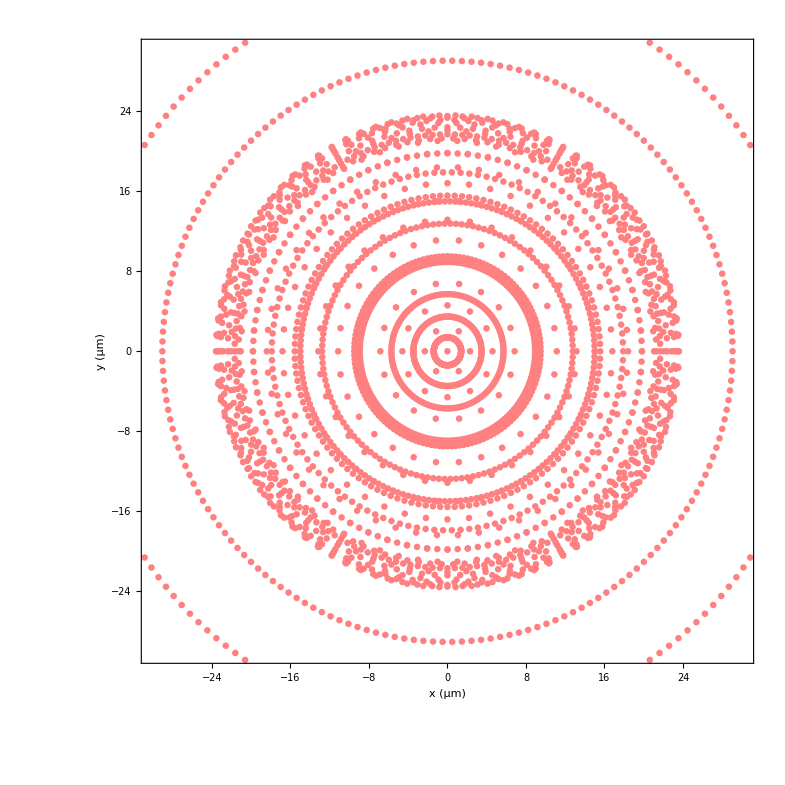

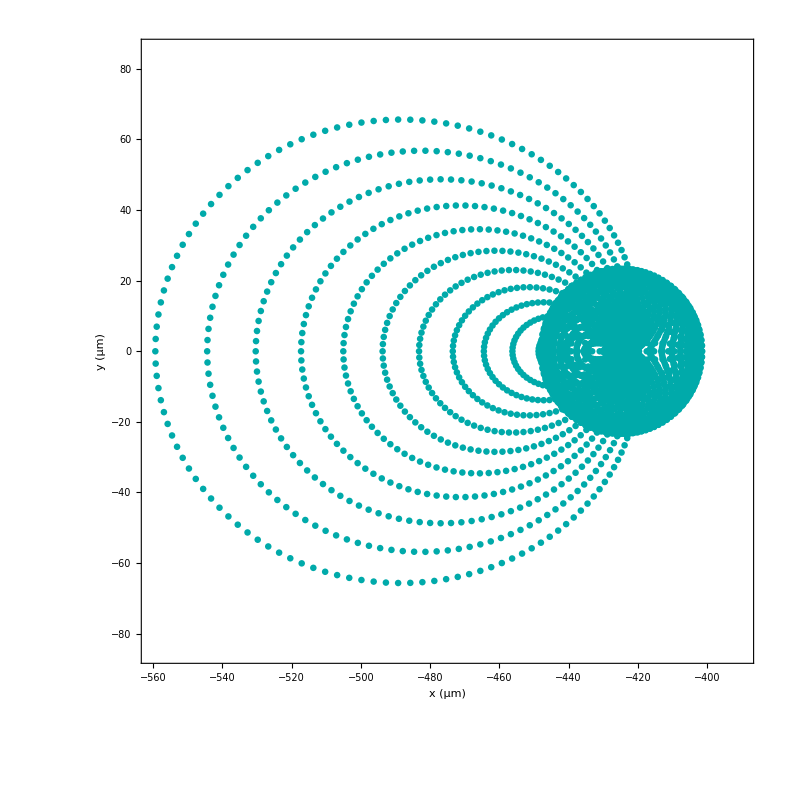

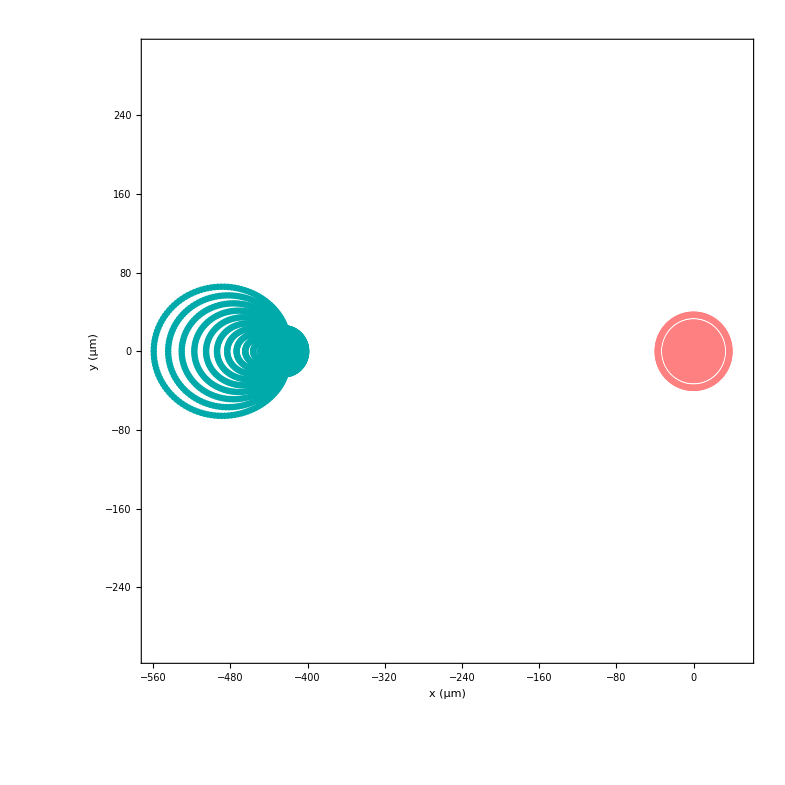

```mathematica
tStart={#[[1]],#[[2]],√(1-#[[1]]^2-#[[2]]^2)}&/@HexapolarGrid[2°,32];(*This generates an hexapolar grid of rays emerging from one point. *)

rcStart={0,0}&/@tStart;

optSystem[tStart,rcStart,ff mm,distBefore1];

lpp1=ListPlot[#[[{1,2}]]&/@intersectionC/um,PlotRange->{{-30,30},{-30,30}},PlotStyle->{Pink,PointSize[0.006]},PlotRangePadding->0,FrameLabel->{"x (μm)","y (μm)"}]
(*This plot the intersection of the rays with the Image plane. We can check that PSF of the system near the optical axis is @ 46 μm. *)
tStart={#[[1]],#[[2]],√(1-#[[1]]^2-#[[2]]^2)}&/@HexapolarGrid[2°,32];

rcStart={1 mm,0}&/@tStart;

optSystem[tStart,rcStart,ff mm,distBefore1];

lpp2=ListPlot[#[[{1,2}]]&/@intersectionC/um,PlotRange->{{-560,-390},{-85,85}},PlotStyle->{Darker@Cyan,PointSize[0.006]},PlotRangePadding->0,FrameLabel->{"x (μm)","y (μm)"}]
Show[lpp1,lpp2,PlotRange-> {{-560,50},{-305,305}},FrameLabel->{"x (μm)","y (μm)"}]
```

Position of the Focal Plane is at:

28.3802

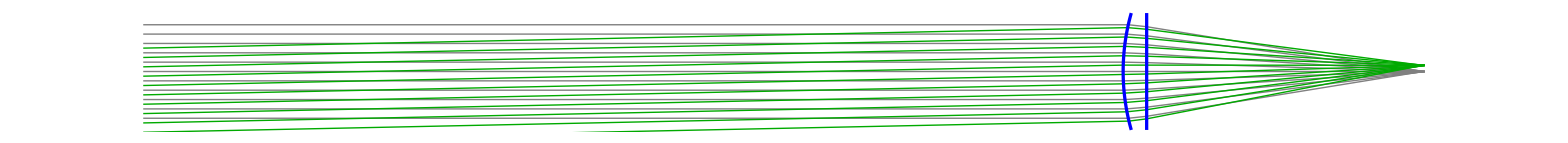

```mathematica
(*Focusing an on axis and off axis beam. *)
rcStart=LineGrid[4mm,400];(*This is an initial grid of rays needed to determine the position of the Focal Plane. *)

tStart={0,0,1}&/@rcStart;

optSystem[tStart,rcStart,0 mm,distBefore1];(*This trace the rays through the system. *)

Print["Position of the Focal Plane is at: "]
ff=FindFocusLine[intersectionC,direction2]/mm(*This determine the focal plane. *)

rcStart=LineGrid[4mm,11];(*This is a grid of rays needed for the drawings (on-axis bundle).  *)

tStart={0,0,1}&/@rcStart;

optSystem[tStart,rcStart,ff mm,distBefore1];

llp1=ListLinePlot[Transpose[#[[All,{3,1}]]&/@{intersectionA,intersection1,intersection2,intersectionC}]/mm,AspectRatio->12/(distBefore1/mm+centerThickness1/mm+ff),PlotStyle->{{Thin,Gray}},Frame-> False,PlotRange->All,ImagePadding->{{5,5},{5,5}}];(*This is a plot of the rays that are parallel to the optical axis.  *)

(*3*)rcStart={#[[1]]-2 mm,#[[2]]}&/@LineGrid[4mm,11];(*This is a grid of rays needed for the drawings (off-axis bundle).  *)

tStart={Sin[1 °],0,Cos[1°]}&/@rcStart;(*The rays defined at (3) are not parallel to the optical axis. *)

optSystem[tStart,rcStart,ff mm,distBefore1];(*This trace the rays not parallel to the optical axis. *)

llp2=ListLinePlot[Transpose[#[[All,{3,1}]]&/@{intersectionA,intersection1,intersection2,intersectionC}]/mm,AspectRatio->10/(distBefore1/mm+centerThickness1/mm+ff),PlotStyle->{{Thin,Darker@Green}},Frame-> False,PlotRange->All,ImagePadding->{{5,5},{5,5}}];(*This is a plot of the rays that are NOT parallel to the optical axis.  *)


Show[(*This is a plot of the whole system. *)
llp1,llp2,
ListLinePlot[{Table[{surface1[x mm,0]/mm,x },{x,-5,5,10/200}],Table[{surface2[x mm,0]/mm,x},{x,-5,5,10/200}]},PlotStyle->{{Blue,Thickness[0.0015]},{Blue,Thickness[0.0015]},{Red,Thickness[0.0015]},{Red,Thickness[0.0015]}}],
ImageSize-> 1800,PlotRange->{{0,(distBefore1/mm+centerThickness1/mm+ff)},{-5,5}},PlotRangePadding-> Scaled[.02]]
```

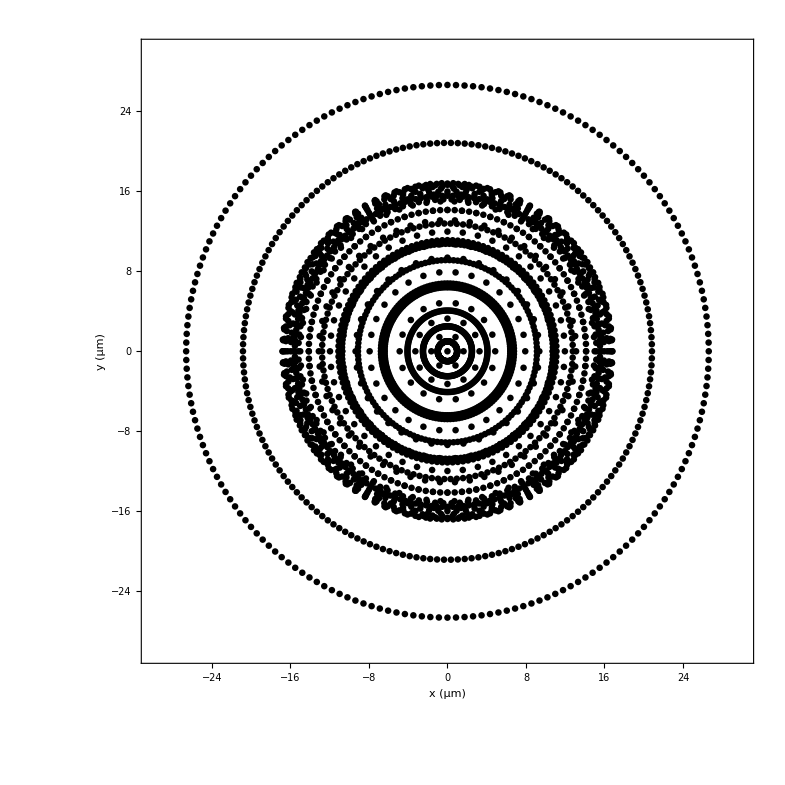

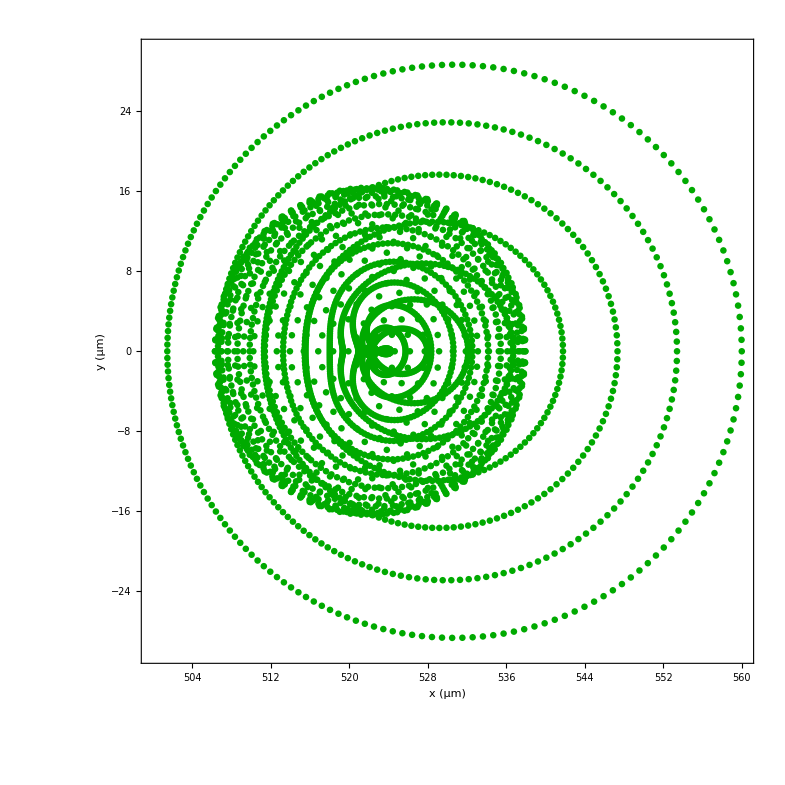

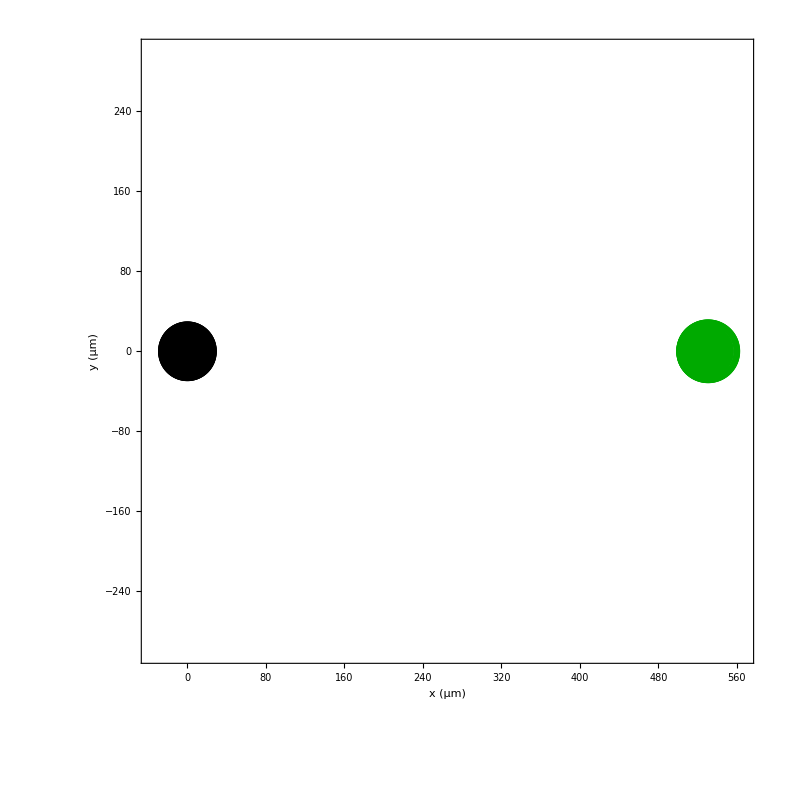

```mathematica
rcStart=HexapolarGrid[4mm,32];

tStart={0,0,1}&/@rcStart;

optSystem[tStart,rcStart,ff mm,distBefore1];

lpp1=ListPlot[#[[{1,2}]]&/@intersectionC/um,PlotRange->{{-30,30},{-30,30}},PlotStyle->{Black,PointSize[0.006]},PlotRangePadding->0,FrameLabel->{"x (μm)","y (μm)"}]
(*This plot the intersection of the rays with the Focal plane. We can check that PSF of the system near the optical axis is @ 33 μm. We conclude that this lens is better for focusing than for image formation. *)
rcStart={#[[1]]-2 mm,#[[2]]}&/@HexapolarGrid[4mm,32];

tStart={Sin[1 °],0,Cos[1°]}&/@rcStart;

optSystem[tStart,rcStart,ff mm,distBefore1];

lpp2=ListPlot[#[[{1,2}]]&/@intersectionC/um,PlotRange->{{500,560},{-30,30}},PlotStyle->{Darker@Green,PointSize[0.006]},PlotRangePadding->0,FrameLabel->{"x (μm)","y (μm)"}]
Show[lpp1,lpp2,PlotRange-> {{-35,565},{-300,300}}]
```

{2.4375,Null}

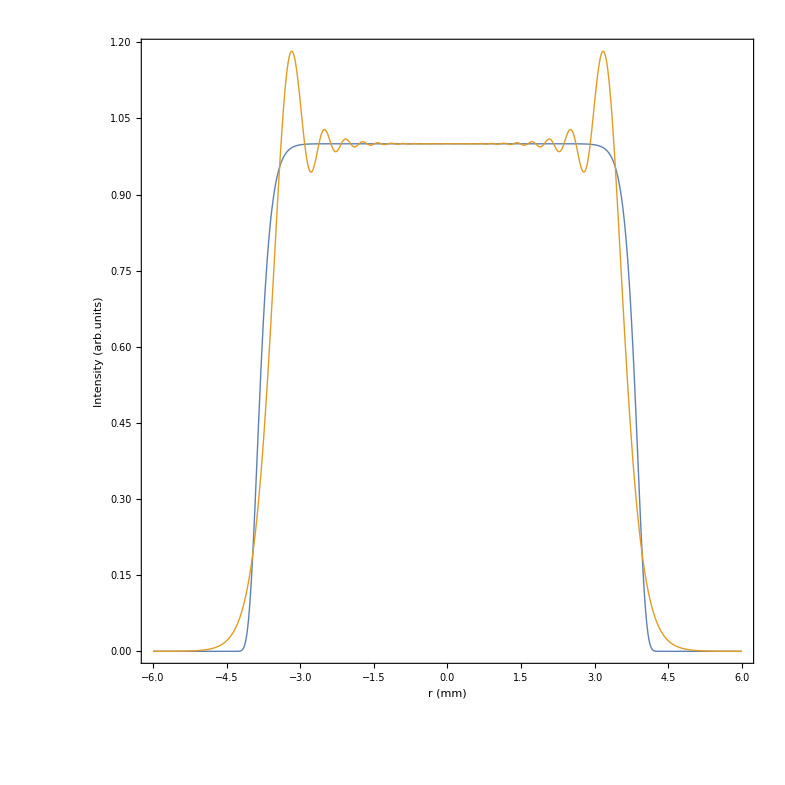

```mathematica
(*Physical Optics Propagation to the Focal Plane Ex. 2.2 *)

(*A top hat beam w= 4 mm is introduced in the system. *)

w=4 mm;
f1[x_,y_]=Exp[-((x^2+y^2)/w^2)^12];(*The beam have the distribution f1 at 1000 mm before the lens.*)

(*Spectrum of Plane Waves (SPW) propagation to the lens.*)
Timing[f2=SPWOperator[4.5 mm,128,1000 mm,"InterpolationOrder"-> 6,"padLevel"-> 3][f1];](*Computation time. *)
(*Please note the ear-like shape of the distribution characteristic to the propagation of the top-hat beam, for example:  *)
(*-Graphics-*)
(*  D. Shealy, and J. Hoffnagle, "Laser beam shaping profiles and propagation," Appl.Opt. 45, 5118-5131 (2006). *)

Plot[{Abs[f1[x mm,0]]^2,Abs[f2[x mm,0]]^2},{x,-6 ,6},PlotRange-> All,FrameLabel->{"r (mm)","Intensity (arb.units)"},PlotRangePadding->{0,Scaled[.05]}]
```

Time needed for Ray Tracing (10000 Rays × 2 Surfaces) is:

{1.20313,Null}

Time needed propagation based on Geometrical optics is:

{1.26563,Null}

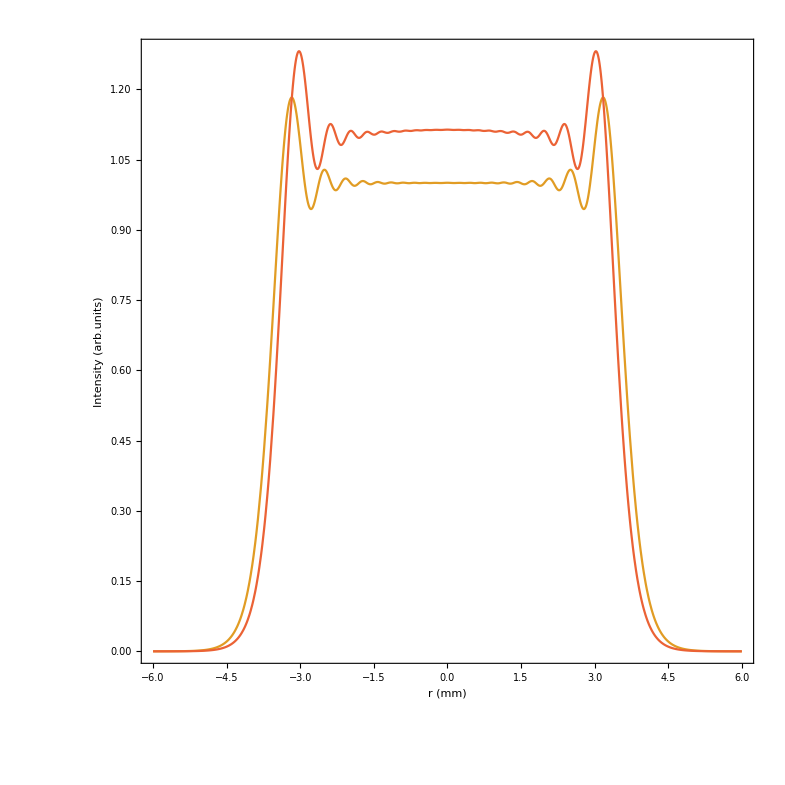

```mathematica
(*Now the beam is traced through the lens using Geometrical Optics.*)

rcStart=LineGrid[4mm,400];

tStart={0,0,1}&/@rcStart;

optSystem[tStart,rcStart,0 mm,distBefore1];

ff=FindFocusLine[intersectionC,direction2]/mm;

rcStart=CartesianGrid[7 mm,100];

tStart={0,0,1}&/@rcStart;

Print["Time needed for Ray Tracing (10000 Rays × 2 Surfaces) is: "]
Timing[optSystem[tStart,rcStart,ff mm,distBefore1];]

ol=FindOpticalPathLength[{intersectionB,intersection1,intersection2},{refIndexAir,refractiveIndex1}];(*Optical path Length is necessary to determine the wavefront of the beam after the lens. *)
(*Please note that this path Length is computed between the plane perpendicular to the optical axis and tangent to the first surface of the lens and the second (plane) surface of the lens. *)
Print["Time needed propagation based on Geometrical optics is: "]
Timing[f3=GeometricOperator[intersectionB,intersection2,ol,"curvatureRadius"->ff mm,"uniformGrid"-> True][f2];](*This Operator compute the optical field after the lens. *)
(*Geometric operator uses the Ray distribution in the input/output plane to compute the intensity and the Optical path Length to compute the phase. "uniformGrid"-> True allows the InterpolationOrder
for the interpolation of the Optical Length to be higher than 1, but this works only if input grid of rays is the CartesianGrid, otherwise the InterpolationOrder will be authomatically set to 1. *)
(*If the optical element is a Lens and the curvature Radius of the beam after the lens is known approximatively, is recomended to use the option "curvatureRadius"-> CurvatureRadius, this will extract an analythical spherical phase from the phase of the beam before the interpolation, this will also smoothen the computed phase. *)
Plot[{Abs[f2[x mm,0]]^2,Abs[f3[x mm,0]]^2},{x,-6,6},PlotRange-> All,PlotStyle-> {ColorData[97,2],ColorData[97,4]},FrameLabel->{"r (mm)","Intensity (arb.units)"},PlotRangePadding->{0,Scaled[.05]}]
```

```mathematica
DensityPlot[Abs[f3[x mm,y mm]]^2,{x,-6 ,6},{y,-6 ,6},PlotPoints->250,MaxRecursion->1,ColorFunction->spectralCF,PlotRange->All,FrameLabel->{"x (mm)","y (mm)"}]
```

{30.2188,Null}

{359.594,Null}

{11.5469,Null}

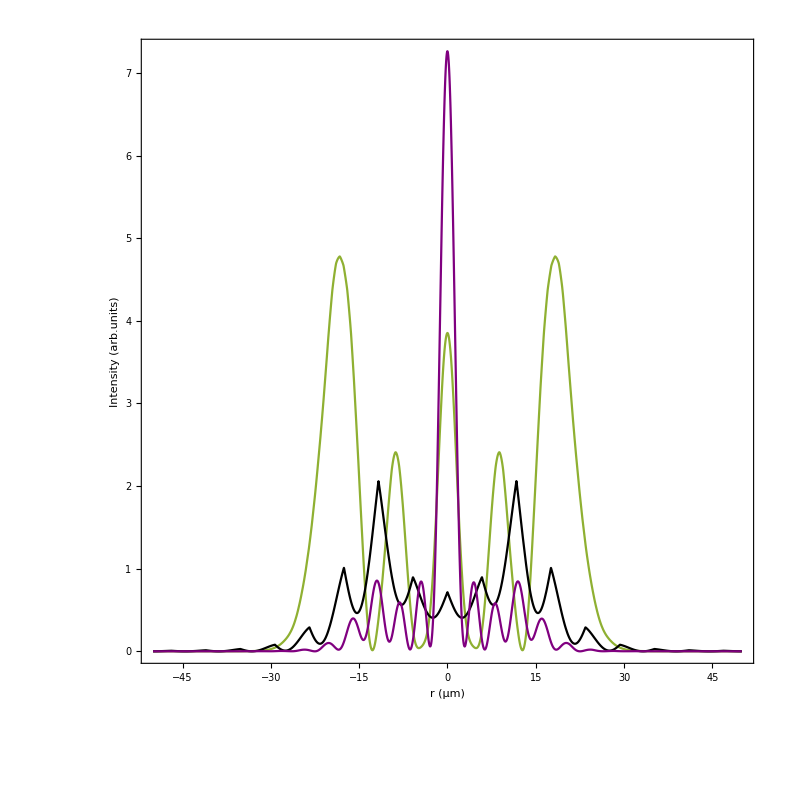

```mathematica
(*Propagation to the Focal Plane.*)

Timing[f4Fresnel=FresnelOperator[6 mm,512,ff mm,"padLevel"-> 3][f3];]
(*In this particular case (NA approx. 0.25 and strong spherical aberation) the FresnelOperator is not accurate because is Paraxial. *)
Timing[f4SPW=SPWOperator[6 mm,2048,ff mm][f3];]
(*Non-Paraxial SPWOperator is extremely unefficient in this case. Even with 8^2 more points the spherical phase cannot be sampled corectly. *)
Timing[f4SASPW=SASPWOperator[6 mm,256,ff mm,"padLevel"-> 2,"paraxialF"->ff mm ][f3];]
(*For cases like this one we have SASPWOperator, implemented according to:
Z. Wang, S. Zhang, O. Baladron-Zorita, C. Hellmann, and F. Wyrowski, "Application of the semi-analytical Fourier transform to electromagnetic modeling," Opt.Express 27,15335-15350 (2019). *)
Plot[{10 Abs[f4Fresnel[x um,0]]^2/10^5,20 Abs[f4SPW[x um,0]]^2/10^5,Abs[f4SASPW[x um,0]]^2/10^5},{x,-50,50},PlotRange-> All,PlotStyle-> {ColorData[97,3],Black,Purple}]
```

```mathematica
rcStart=LineGrid[4mm,400];

tStart={0,0,1}&/@rcStart;

optSystem[tStart,rcStart,0 mm,distBefore1];

ff=FindFocusLine[intersectionC,direction2]/mm;


rcStart=CartesianGrid[10mm,100];

tStart={0,0,1}&/@rcStart;

optSystem[tStart,rcStart,ff mm,distBefore1];

ol=FindOpticalPathLength[{intersectionB,intersection1,intersection2,intersectionC},{refIndexAir,refractiveIndex1,refIndexAir}];

f5=AmplitudeGeometricOperator[intersectionB,intersection2,"uniformGrid"-> True][f2];
(*Furthermore we have the experimental version of scalarRSFOperator.*)
Timing[f6=scalarRSFOperator[intersectionC,direction2,ol,6 mm,128,ff mm,"padLevel"-> 2][f5];]
```

{1.89063,Null}

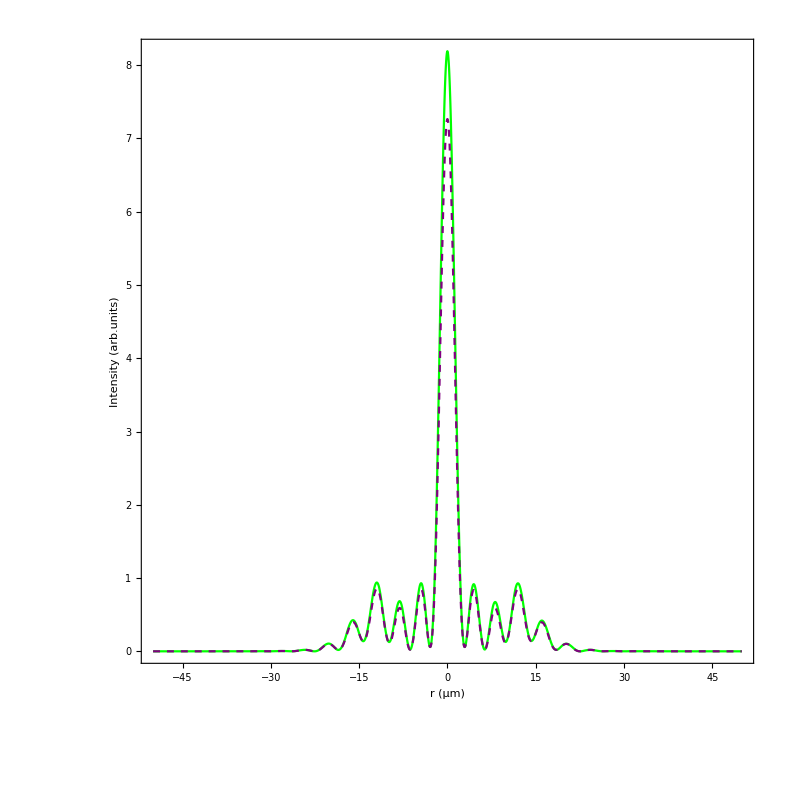

```mathematica
Plot[{Abs[f6[x um,0]]^2/10^5,Abs[f4SASPW[x um,0]]^2/10^5},{x,-50,50},PlotRange-> All,PlotStyle-> {{Green},{Purple,Dashed}}]
```

```mathematica
DensityPlot[Abs[f4SASPW[x um,y um]]^2/10^5,{x,-30,30},{y,-30,30},PlotPoints->250,MaxRecursion->1,ColorFunction->jetMLVWO,PlotRange->All]
lpp1(*The focal spot is strongly affected by the sperical aberration of the lens. Here is the Focal Spot and the Ray Spot Diagram cor comparison. *)
```

-Graphics-

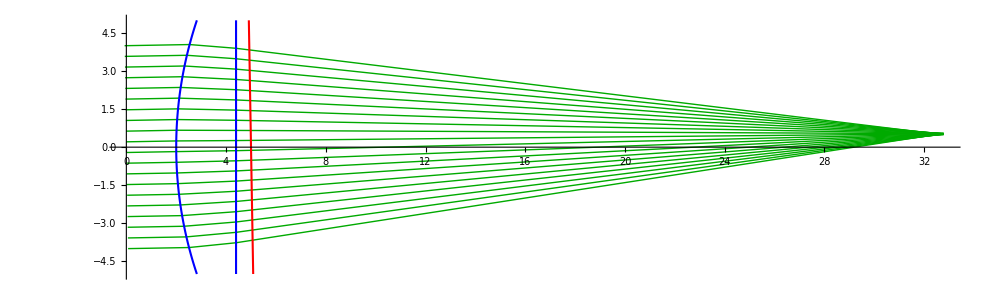

{71.0938,Null}

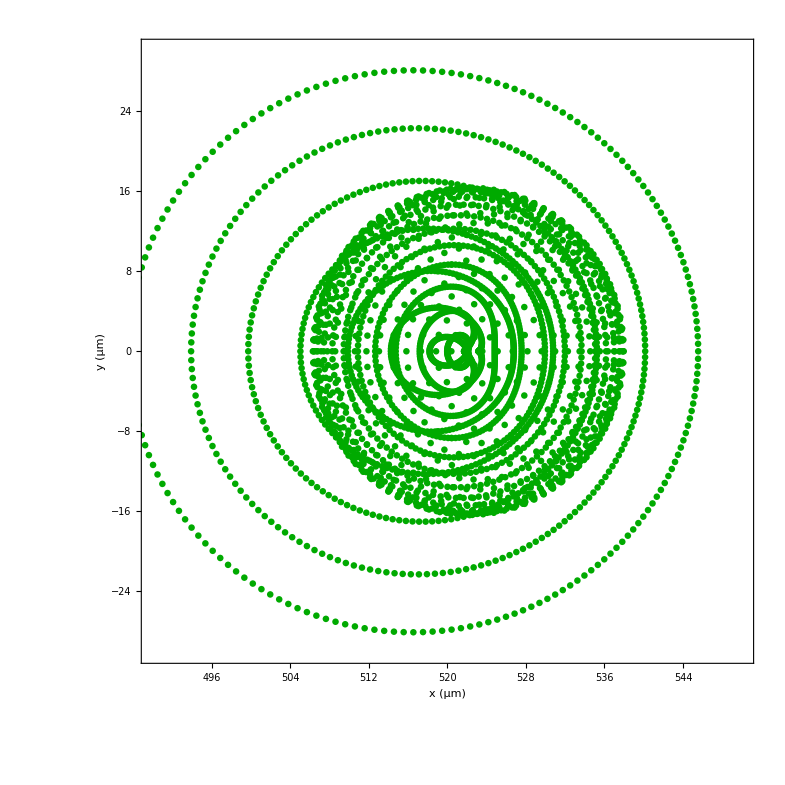

```mathematica
(*Focusing an on axis and off axis beam.*)

distBefore1=2 mm;

rcStart=LineGrid[4mm,400];

tStart={0,0,1}&/@rcStart;

optSystem[tStart,rcStart,0 mm,distBefore1];

ff=FindFocusLine[intersectionC,direction2]/mm;

α=1°;
rcStart=Map[({{Cos[α], 0}, {0, 1}, {-Sin[α], 0}}).#&,LineGrid[4mm,20]];
tStart={Sin[α],0,Cos[α]}&/@rcStart;

optSystem[tStart,rcStart,ff mm,distBefore1,"tiltedRays"-> True];

llp2=ListLinePlot[Transpose[#[[All,{3,1}]]&/@{intersectionA,intersection1,intersection2,intersectionC}]/mm,AspectRatio->10/(distBefore1/mm+centerThickness1/mm+ff),PlotStyle->{{Thin,Darker@Green}},Frame-> False,PlotRange->All,ImagePadding->{{5,5},{5,5}}];

Show[
llp2,

ListLinePlot[{Table[{surface1[x mm,0]/mm,x },{x,-5,5,10/200}],Table[{surface2[x mm,0]/mm,x},{x,-5,5,10/200}],Table[{surface3[x mm,0]/mm,x},{x,-5,5,10/200}]},PlotStyle->{{Blue,Thickness[0.0015]},{Blue,Thickness[0.0015]},{Red,Thickness[0.0015]},{Red,Thickness[0.0015]}}],
ImageSize-> 1000,PlotRange->{{0,(distBefore1/mm+centerThickness1/mm+ff)},{-5,5}},PlotRangePadding-> Scaled[.02],Axes-> {True,False}]

rcStart=Map[({{Cos[α], 0}, {0, 1}, {-Sin[α], 0}}).#&,CartesianGrid[7mm,100]];(*Using a tilted grid of rays we can directly simulate the propagation of a beam tilted with respect to the optical axis. *)
tStart={Sin[α],0,Cos[α]}&/@rcStart;

optSystem[tStart,rcStart,ff mm,distBefore1,"tiltedRays"-> True];

f5=AmplitudeGeometricOperator[intersectionA,intersection2,"uniformGrid"-> True][f2];

ol=FindOpticalPathLength[{intersectionA,intersection1,intersection2,intersectionC},{refIndexAir,refractiveIndex1,refIndexAir}];

Timing[f6=scalarRSFOperator[intersectionC,direction2,ol,6 mm,1024,ff mm,"padLevel"-> 2][f5];](*Many points are needed to sample the strong linear phase caused by the tilt. *)

DensityPlot[Abs[f6[x um,y um]]^2/10^5,{x,490,550},{y,-30,30},PlotPoints->250,MaxRecursion->1,ColorFunction->jetMLVWP,PlotRange->All]
rcStart=Map[({{Cos[α], 0}, {0, 1}, {-Sin[α], 0}}).#&,HexapolarGrid[4 mm,32]];
tStart={Sin[α],0,Cos[α]}&/@rcStart;

optSystem[tStart,rcStart,ff mm,distBefore1,"tiltedRays"-> True];

lpp2=ListPlot[#[[{1,2}]]&/@intersectionC/um,PlotRange->{{490,550},{-30,30}},PlotStyle->{Darker@Green,PointSize[0.006]},PlotRangePadding->0,FrameLabel->{"x (μm)","y (μm)"}]
```

```mathematica
distBefore1=2 mm;

rcStart=LineGrid[4mm,400];

tStart={0,0,1}&/@rcStart;

optSystem[tStart,rcStart,0 mm,distBefore1];

ff=FindFocusLine[intersectionC,direction2]/mm;

α=1°;
rcStart=Map[({{Cos[α], 0}, {0, 1}, {-Sin[α], 0}}).#&,CartesianGrid[5mm,100]];
tStart={Sin[α],0,Cos[α]}&/@rcStart;

optSystem[tStart,rcStart,ff mm,distBefore1,"tiltedRays"-> True];

f5=AmplitudeGeometricOperator[intersectionA,intersection2,"uniformGrid"-> True][f2];

ol=FindOpticalPathLength[{intersectionA,intersection1,intersection2,intersectionC},{refIndexAir,refractiveIndex1,refIndexAir}]-Sin[α]*ff mm Map[#[[1]]&,direction2];
(*It is recomended to extract the linear phase according to frequency shifting theorem of Fourier transforms. This may improve the computation time up to 50 times. *)
Timing[f6=scalarRSFOperator[intersectionC,direction2,ol,6 mm,128,ff mm ,"padLevel"-> 2][f5];]

DensityPlot[Abs[f6[x um-Sin[α]*ff mm,y um]]^2/10^5,{x,490,550},{y,-30,30},PlotPoints->250,MaxRecursion->1,ColorFunction->jetMLVWP,PlotRange->All]
```

{2.71875,Null}

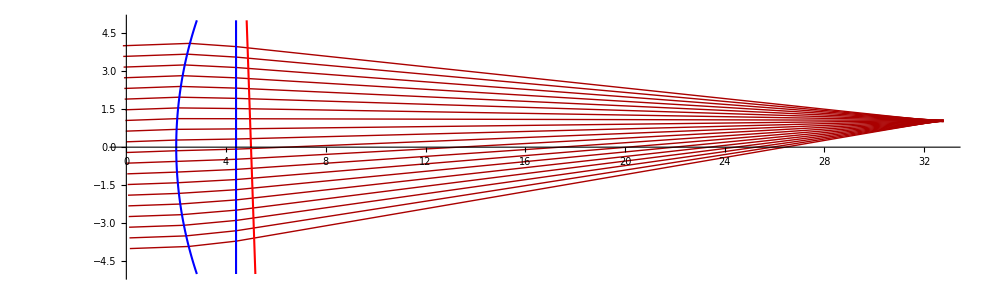

{147.219,Null}

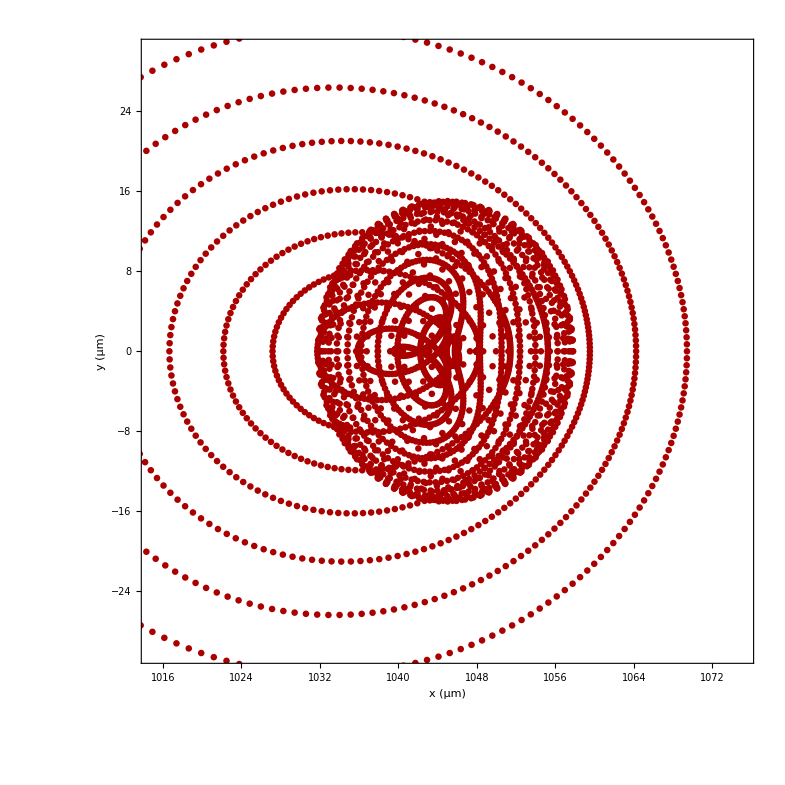

```mathematica
distBefore1=2 mm;

rcStart=LineGrid[4mm,400];

tStart={0,0,1}&/@rcStart;

optSystem[tStart,rcStart,0 mm,distBefore1];

ff=FindFocusLine[intersectionC,direction2]/mm;

α=2°;
rcStart=Map[({{Cos[α], 0}, {0, 1}, {-Sin[α], 0}}).#&,LineGrid[4mm,20]];
tStart={Sin[α],0,Cos[α]}&/@rcStart;

optSystem[tStart,rcStart,ff mm,distBefore1,"tiltedRays"-> True];

llp2=ListLinePlot[Transpose[#[[All,{3,1}]]&/@{intersectionA,intersection1,intersection2,intersectionC}]/mm,AspectRatio->10/(distBefore1/mm+centerThickness1/mm+ff),PlotStyle->{{Thin,Darker@Red}},Frame-> False,PlotRange->All,ImagePadding->{{5,5},{5,5}}];

Show[
llp2,

ListLinePlot[{Table[{surface1[x mm,0]/mm,x },{x,-5,5,10/200}],Table[{surface2[x mm,0]/mm,x},{x,-5,5,10/200}],Table[{surface3[x mm,0]/mm,x},{x,-5,5,10/200}]},PlotStyle->{{Blue,Thickness[0.0015]},{Blue,Thickness[0.0015]},{Red,Thickness[0.0015]},{Red,Thickness[0.0015]}}],
ImageSize-> 1000,PlotRange->{{0,(distBefore1/mm+centerThickness1/mm+ff)},{-5,5}},PlotRangePadding-> Scaled[.02],Axes-> {True,False}]

rcStart=Map[({{Cos[α], 0}, {0, 1}, {-Sin[α], 0}}).#&,CartesianGrid[7mm,100]];
tStart={Sin[α],0,Cos[α]}&/@rcStart;

optSystem[tStart,rcStart,ff mm,distBefore1,"tiltedRays"-> True];

f5=AmplitudeGeometricOperator[intersectionA,intersection2,"uniformGrid"-> True][f2];

ol=FindOpticalPathLength[{intersectionA,intersection1,intersection2,intersectionC},{refIndexAir,refractiveIndex1,refIndexAir}];

Timing[f6=scalarRSFOperator[intersectionC,direction2,ol,6 mm,1536,ff mm,"padLevel"-> 2][f5];]

DensityPlot[Abs[f6[x um,y um]]^2/10^5,{x,1015,1075},{y,-30,30},PlotPoints->250,MaxRecursion->1,ColorFunction->jetMLV18,PlotRange->All]
rcStart=Map[({{Cos[α], 0}, {0, 1}, {-Sin[α], 0}}).#&,HexapolarGrid[4 mm,32]];
tStart={Sin[α],0,Cos[α]}&/@rcStart;

optSystem[tStart,rcStart,ff mm,distBefore1,"tiltedRays"-> True];

lpp2=ListPlot[#[[{1,2}]]&/@intersectionC/um,PlotRange->{{1015,1075},{-30,30}},PlotStyle->{Darker@Red,PointSize[0.006]},PlotRangePadding->0,FrameLabel->{"x (μm)","y (μm)"}]
```

```mathematica
distBefore1=2 mm;

rcStart=LineGrid[4mm,400];

tStart={0,0,1}&/@rcStart;

optSystem[tStart,rcStart,0 mm,distBefore1];

ff=FindFocusLine[intersectionC,direction2]/mm;

α=2°;
rcStart=Map[({{Cos[α], 0}, {0, 1}, {-Sin[α], 0}}).#&,CartesianGrid[5mm,100]];
tStart={Sin[α],0,Cos[α]}&/@rcStart;

optSystem[tStart,rcStart,ff mm,distBefore1,"tiltedRays"-> True];

f5=AmplitudeGeometricOperator[intersectionA,intersection2,"uniformGrid"-> True][f2];

ol=FindOpticalPathLength[{intersectionA,intersection1,intersection2,intersectionC},{refIndexAir,refractiveIndex1,refIndexAir}]-Sin[α]*ff mm Map[#[[1]]&,direction2];

Timing[f6=scalarRSFOperator[intersectionC,direction2,ol,6 mm,128,ff mm ,"padLevel"-> 2][f5];]

DensityPlot[Abs[f6[x um-Sin[α]*ff mm,y um]]^2/10^5,{x,1015,1075},{y,-30,30},PlotPoints->250,MaxRecursion->1,ColorFunction->jetMLV18,PlotRange->All]
```

{2.78125,Null}

```mathematica
(*Bessel Beam/ Ring Beam generation using an axicon with rounded tip Ex. 2.3 *)

optSystem[rayCoordinateStart_]:=Module[{},

refractiveIndex1=nUVFS800;
centerThickness1=5.2 mm;

surface1[x_,y_]=0.05;
surface2[x_,y_]=surface1[0,0]+centerThickness1-Axz[x,y,0.025 mm,1(*This is the angle of the axicon in ° *)];(*The Conical surface with rounded tip. *)

DxSurface1[x_,y_]=D[surface1[x,y],x];
DySurface1[x_,y_]=D[surface1[x,y],y];
DxSurface2[x_,y_]=D[surface2[x,y],x];
DySurface2[x_,y_]=D[surface2[x,y],y];

rZ0=MapThread[0&,Transpose@rayCoordinateStart];
rayTiltStart={0,0,1}&/@rayCoordinateStart;

intersectionA=Flatten/@Transpose[{rayCoordinateStart,rZ0}];

intersectionB=SurfaceIntersection[rayCoordinateStart,rZ0,rayTiltStart][surface1[0,0]&,0&,0&];

intersection1=SurfaceIntersection[rayCoordinateStart,rZ0,rayTiltStart][surface1,DxSurface1,DySurface1];
Do[intersection1=SurfaceIntersection[intersection1,{},rayTiltStart][surface1,DxSurface1,DySurface1];,10];

direction1=DirectionIn[intersection1,rayTiltStart,refractiveIndex1][DxSurface1,DySurface1];

intersection2=SurfaceIntersection[intersection1,{},direction1][surface2,DxSurface2,DySurface2];
Do[intersection2=SurfaceIntersection[intersection2,{},direction1][surface2,DxSurface2,DySurface2];,10];

direction2=DirectionOut[intersection2,direction1,refractiveIndex1][DxSurface2,DySurface2];

intersectionD=SurfaceIntersection[intersection2,{},direction2][surface2[0,0]&,0&,0&];

intersectionE=SurfaceIntersection[intersection2,{},direction2][(surface2[0,0]+1)&,0&,0&];
]
```

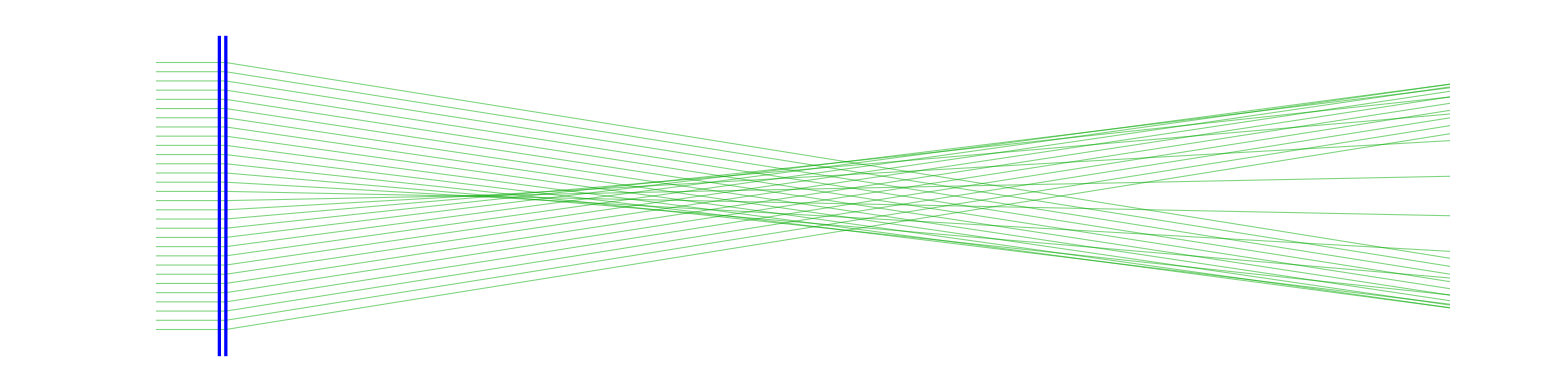

```mathematica
rcStart=LineGrid[5 mm,30];
optSystem[rcStart];
graph=Show[(*Propagation of rays through the system (x/z not same scale). The central part of the axicon have the efect of a spherical lens.*)

ListLinePlot[Transpose[#[[All,{3,1}]]&/@{intersectionA,intersection1,intersection2,intersectionE}]/mm,AspectRatio->1/4,PlotStyle->{{Thickness[0.0005],Darker@Green,Opacity[0.5]}},Frame-> False,PlotRange->All,ImagePadding->{{5,5},{5,5}}],
ListLinePlot[{Table[{surface1[x mm,0]/mm,x },{x,-6 ,6,12/20}],Table[{surface2[x mm,0]/mm,x},{x,-6 ,6,12/20}]},PlotStyle->{{Blue,Thickness[0.0015]},{Blue,Thickness[0.0015]},{Red,Thickness[0.0015]},{Red,Thickness[0.0015]}}],ImageSize-> 1700,PlotRange-> {{-10,1000},{-6,6}}]
```

```mathematica
rcStart=HexapolarGrid[4 mm,70];
optSystem[rcStart];
lpp1=ListPlot[{ArcSin@#[[1]],ArcSin@#[[2]]}&/@direction2*180/π,PlotRangePadding->Scaled[.05],PlotRange-> All,FrameLabel->{"θx ( °)","θy ( °)"},PlotMarkers->"×",PlotStyle->Red](*The directions of the rays after the axicon. *)
lpp2=ListPlot[#[[{1,2}]]&/@intersectionE/mm,PlotRangePadding->0,PlotRange-> {{-5,5},{-5,5}},FrameLabel->{"x (mm)","y (mm)"},PlotMarkers->"×",PlotStyle->Black]
(*The intersection of the rays with a screen placed at 1055.175 mm from the plane on which the input coordinates are defined (1 meter from the tip of the axicon).*)
```

```mathematica
f7[x_,y_]=If[√(x^2+y^2)≥ 8 mm,0,Exp[-(x^2+y^2)/(4 mm)^2]];

rcStart=CartesianGrid[8 mm,100];
time=AbsoluteTime[];
optSystem[rcStart];

ol=FindOpticalPathLength[{intersectionB,intersection1,intersection2,intersectionD},{refIndexAir,refractiveIndex1,refIndexAir}];
f8=GeometricOperator[intersectionB,intersectionD,ol,"uniformGrid"-> True][f7];

time-AbsoluteTime[]
```

-6.5245332

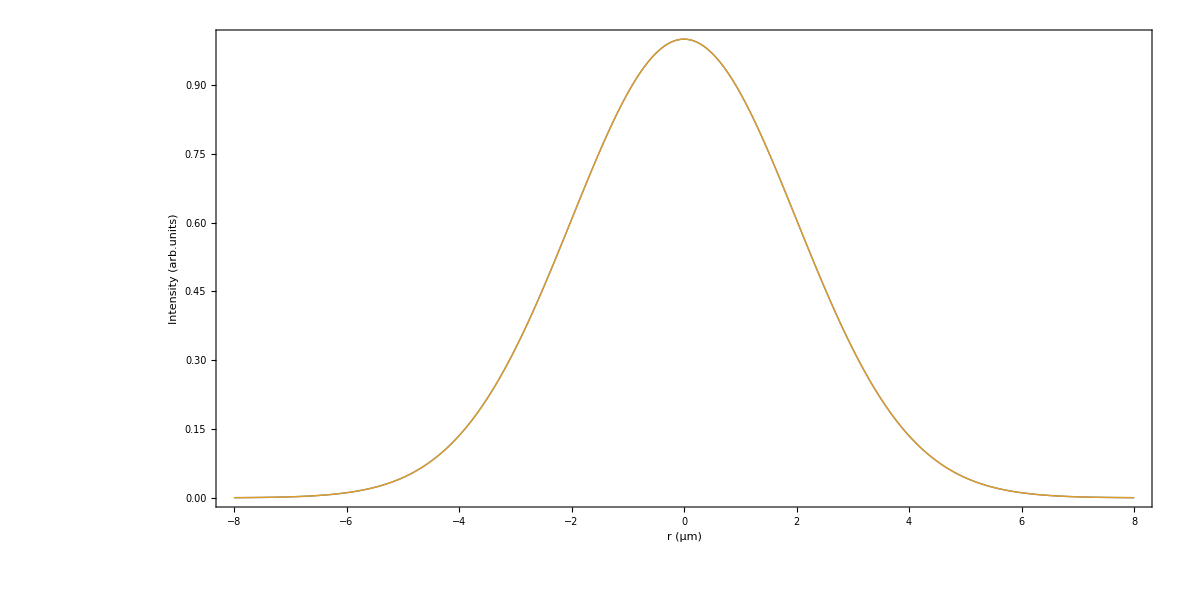

```mathematica
(*The input beam and the beam computed on a plane surface that is tangent on the conical surface of the axicon are compared.*)
(*Intensity distributions*)
Plot[{Abs[f7[x mm,um]]^2,Abs[f8[x mm,um]]^2},{x,-8,8},PlotPoints-> 300,AspectRatio->1/2,ImageSize->1200]
```

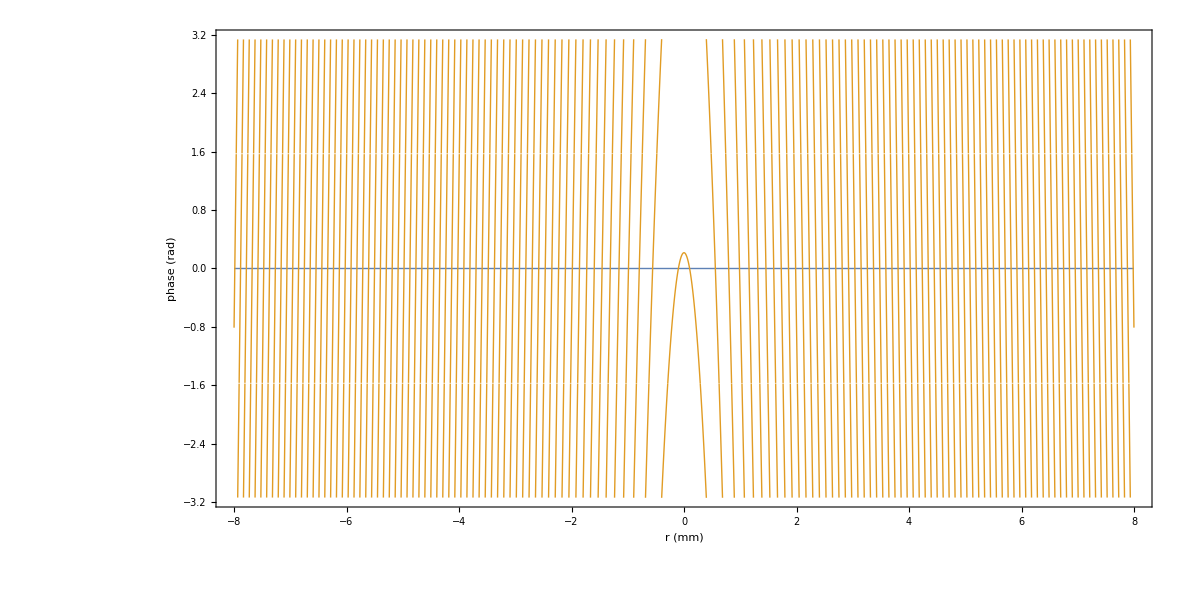

```mathematica
(*and phase. The phase is nearly linear with √(x^2+y^2). We need a high number of points to sample this phase. *)
Plot[{Arg[f7[x mm,um]],Arg[f8[x mm,um]]},{x,-8,8},PlotPoints-> 3000,AspectRatio->1/2,ImageSize->1200,FrameLabel->{"r (mm)","phase (rad)"}]
```

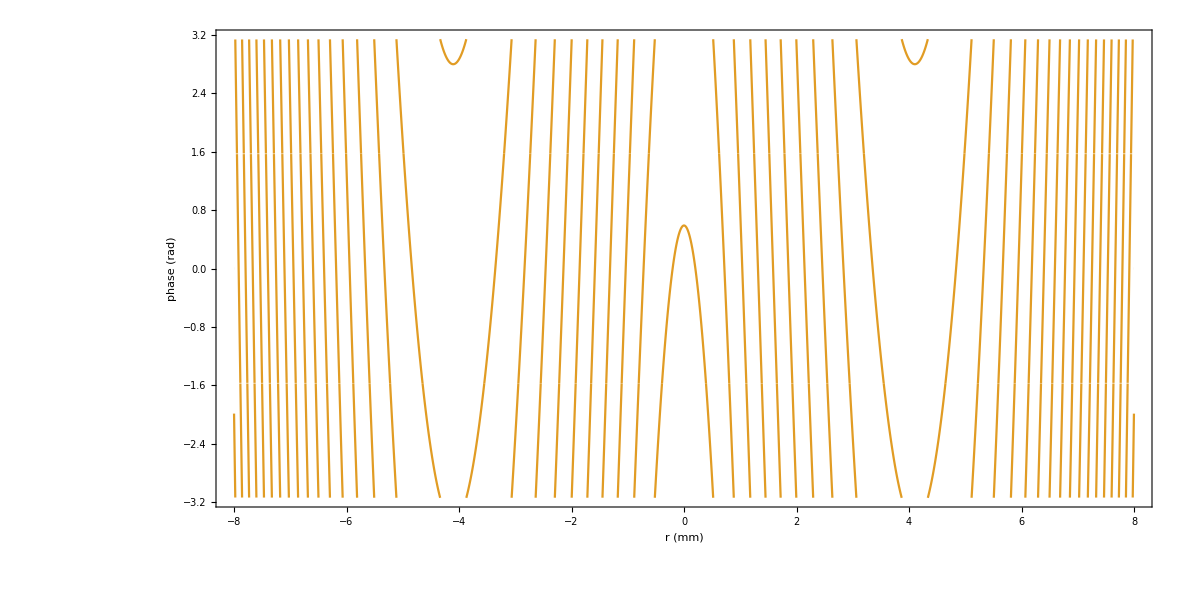

```mathematica
(*Here is the phase induced by the axicon with the quadratic phase of the Fresnel Kernel for z = 550 mm. It shows that it would not be dificult to sample the phase for Fresnel propagation to 550 mm from the axicon. *)
Plot[{Arg[f8[x mm,um]Exp[ⅈ k0 (x mm)^2/(2 550 mm)]]},{x,-8,8},PlotPoints-> 3000,AspectRatio->1/2,ImageSize->1200,FrameLabel->{"r (mm)","phase (rad)"},PlotStyle-> ColorData[97,2]]
```

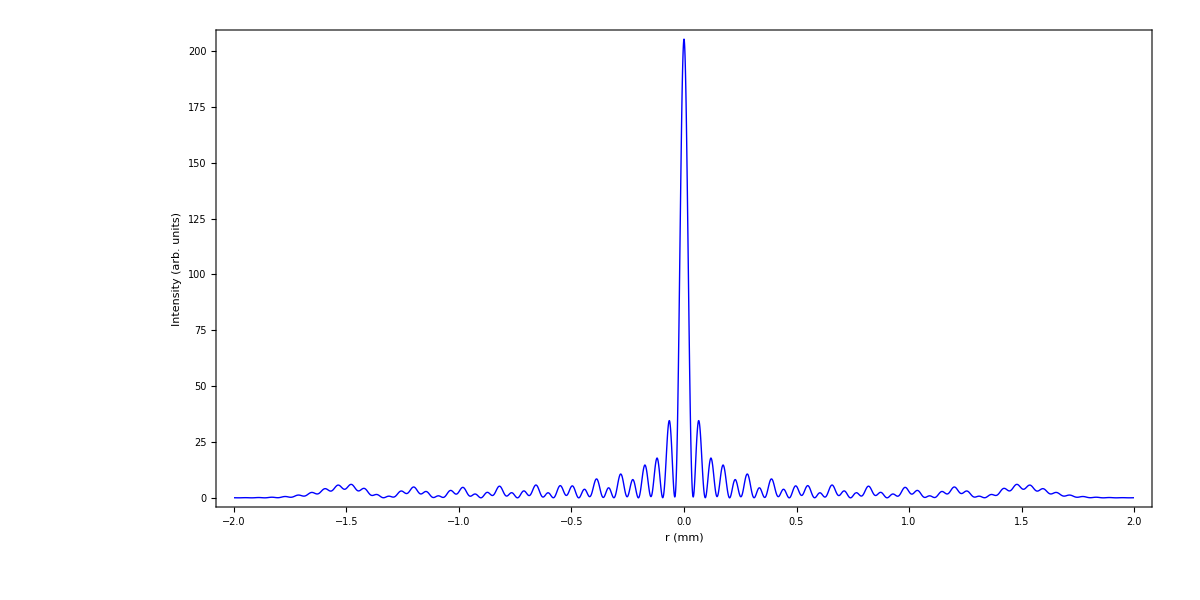

```mathematica
f8b[x_,y_]=If[√(x^2+y^2)≥ 8 mm,0,f8[x,y]];
f9=FresnelOperator[8 mm,1024,550 mm,"padLevel"-> 3][f8b];(*Fresnel Propagation.*)
(*The Bessel beam formed at 550 mm from the axicon. *)
Plot[Abs[f9[x mm,um]]^2,{x,-2,2},PlotPoints-> 1536,PlotRange->All,PlotStyle->{Blue,Thin},AspectRatio->1/2,ImageSize->1200,FrameLabel->{"r (mm)","Intensity (arb. units)"}]
```

```mathematica
fz=SPWOperator[2 mm,768,-1 mm,"padLevel"-> 3,"nrSteps"-> 350][f9];
(*We use the fact that the beam have a smaller spatial extension to make the grid finer for backward SPW Propagation. *)
pl=DensityPlot[Abs[fz[z mm-349 mm-256.2 mm,x mm]]^2,{z,256.2,349+256.2},{x,-4,4},ColorFunction->(GBPCF[#^0.4]&),FrameLabel-> {"z (mm)","x (mm)"},PlotPoints-> {200,300},MaxRecursion->2,PlotRange->All]
```

```mathematica
(*The Intensity distribution in x z plane, as in the figure above, overlaped on the ray distribution. *)
Show[pl[[1]],graph,AspectRatio->1/4,PlotStyle->{{Thickness[0.0015],Green,Opacity[0.5]}},Frame-> False,PlotRange-> {{-10,1000},{-6,6}},ImagePadding->{{5,5},{5,5}},ImageSize-> 1700]
```

```mathematica
f10=SPWOperator[3 mm,1536,(1055.175-600 )mm,"padLevel"-> 2][f9];(*Propagation to a plane screen placed at 1 meter from the tip of the axicon. *)
```

```mathematica
(*Ring Beam formed at 1 meter from the tip of the axicon, comparison with the Ray distribution in the same plane.  *)
DensityPlot[Abs[f10[x mm,y mm]]^2,{x,-5,5},{y,-5 ,5},PlotPoints->300,MaxRecursion->2,ColorFunction->beamprofilerCF2,PlotRange->All,FrameLabel->{"x (mm)","y (mm)"}]
```